```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]]
```

√(om/a^3+(1-om) efe[a])

```mathematica
omegam[a_]=om/(a^3 e[a]^2)
```

om/(a^3 (om/a^3+(1-om) efe[a]))

```mathematica
gamma[a_]=gamma0+gammap0(1/a-1)
```

gamma0+(-1+1/a) gammap0

```mathematica
f[a_]=omegam[a]^gamma[a]
```

(om/(a^3 (om/a^3+(1-om) efe[a])))^(gamma0+(-1+1/a) gammap0)

```mathematica
f[2]
```

8^(-gamma0+gammap0/2) (om/(om/8+(1-om) efe[2]))^(gamma0-gammap0/2)

```mathematica
om=0.3;
gamma0=0.55;
gammap0=-0.01;
```

```mathematica
sol= NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}]
```

{{efe→InterpolatingFunction[…]}}

```mathematica
Fa[a_]= efe[a]/.Flatten[sol]
```

InterpolatingFunction[…][a]

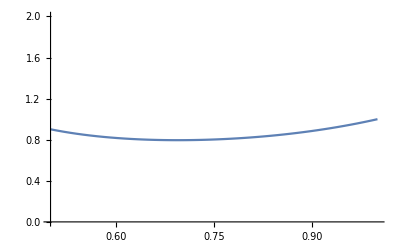

```mathematica
Plot[Fa[a],{a,0.5,1}, PlotRange->{0,2}]
```

```mathematica
Fz[z_]:=Fa[1/(1+z)]
```

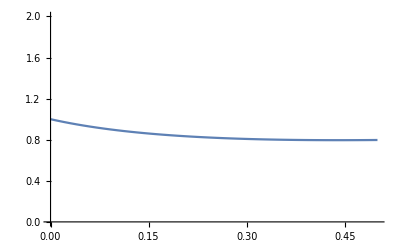

```mathematica
Plot[Fz[z],{z,0,0.5},PlotRange->{0,2}]
```

```mathematica
w[z_]:=Fz'[z]/Fz[z] 1/3(1+z)-1
```

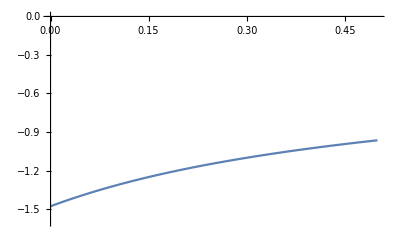

```mathematica
Plot[w[z],{z,0,0.5}, PlotRange->{-1.6,0}]
```

```mathematica
ez[z_]:=Sqrt[om(1+z)^3+(1-om)Fz[z]]
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z]
```

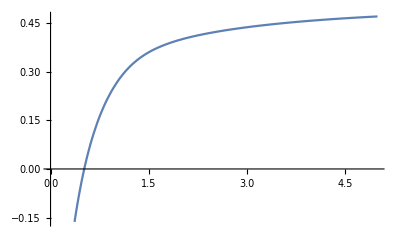

```mathematica
Plot[q[z],{z,0,5}]
```

```mathematica
q[0]
```

-1.05202